```mathematica
AppendTo[$Path,"/Users/Daan/Documents/GitHub/self-organising-regulation/mathematica_notebooks_minimal_GRDS_model/"];
<<plottingfunctions`
pars={ϕ->0.5,f->0.1,T->10};
SetOptions[{Plot, ListLinePlot, ListPlot,Plot3D,DensityPlot,LogLogPlot,LogLinearPlot,LogPlot, RegionPlot}, {PlotTheme->{"Scientific","SansLabels","VibrantColor"}}];
SetOptions[{Plot, ListLinePlot, ListPlot, ContourPlot,DensityPlot,LogLogPlot,LogLinearPlot,LogPlot, RegionPlot}, {Frame->True,BaseStyle->{FontSize->20,FontFamily->"Helvetica"}, FrameStyle->Black,LabelStyle->{Black,FontSize->16,FontFamily->"Helvetica"}}];
SetOptions[{Plot3D}, {BaseStyle->{FontSize->16,FontFamily->"Helvetica"}}];
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
Offpaclet:ref/Off[FindMinimum::reged]
Offpaclet:ref/Off[FindMaximum::reged]
colormaps={"Default"->97,"Earth"->98,"Garnet"->99,"Opal"->100,"Sapphire"->101,"Steel"->102,"Sunrise"->103,"Textbook"->104,"Water"->105,"BoldColor"->106,"CoolColor"->107,"DarkColor"->108,"MarketingColor"->109,"NeonColor"->109,"PastelColor"->110,"RoyalColor"->111,"VibrantColor"->112,"WarmColor"->113};
(*Apple colors*)blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
(*4 Apple colors*)
apple4={green,red,grey,purple};
```

RefLink[Off,paclet:ref/Off][The point `1` is at the edge of the search region `3` in coordinate `2` and the computed search direction points outside the region.]

RefLink[Off,paclet:ref/Off][The point `1` is at the edge of the search region `3` in coordinate `2` and the computed search direction points outside the region.]

```mathematica
GLOBALPARS={MAXPHI->999,PLOTPOINTS->30};
```

## Derivations without GRDS

We solve the system described in Equation [2] of the main text . We simulate the growth of the number of cells in an adapted phenotype n_g and in a non-adapted phenotype, respectively with growth rate μ=1 and one with growth rate μ=0. Cells can switch between the phenotypes: the switching rate from fast to slow is ϕ, and the switching rate from slow to fast is ϕ/n. In this notebook, we will (for analytical purposes) often use f:=1/n with 0<f<1. Initially, the population has a fraction p_0 in the fast phenotype, and the duration of one environment is given by T. We get the  following analytical solution:

```mathematica
analyticalSol = DSolve[{sg'[t] == (1 -ϕ) sg[t]+f ϕ sb[t],sb'[t]== -f ϕ sb[t]+ϕ sg[t],sg[0]==p0 ,sb[0]==(1-p0) },{sg[t],sb[t]},t];
```

This solution can be simplified somewhat by using information about our parameters in the FullSimplify-command.

```mathematica
analyticalSol2 = FullSimplify[analyticalSol,Assumptions -> {p0>0,p0<1,f>0,f<1,ϕ>0,t≥0}]
```

{{sb[t]→1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (1+(-1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))-p0 (1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+p0+(1+f (-1+p0)+p0) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))-p0 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))),sg[t]→1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (2 (-1+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) f ϕ+p0 (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))))}}

We can gather these solutions in a vector s(ϕ,f,p0,t),

```mathematica
s[ϕ_,f_,p0_,t_]:=Evaluate[{sg[t],sb[t]}/.analyticalSol2[[1]]]
```

And the total population size is then given by the dot product with the vector [1,1]:

```mathematica
stot[ϕ_,f_,p0_,t_]:=Evaluate[FullSimplify[s[ϕ,f,p0,t].{1,1},Assumptions->{ϕ>0,t≥0,p0>0,p0<1,f>0,f<1}]]
stot[ϕ,f,p0,t]
```

1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (1-2 p0-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))

Using these functions, we can calculate the fraction of the population in the good state at time t.

```mathematica
frac[ϕ_,f_,p0_,t_]:=Evaluate[FullSimplify[s[ϕ,f,p0,t][[1]]/stot[ϕ,f,p0,t],Assumptions -> {f>0,f<1,p0>0,p0<1,ϕ>0,t>=0}]]
frac[ϕ,f,p0,t]
```

(2 (-1+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) f ϕ+p0 (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))))/(1-2 p0-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))

### Analysis of the fraction of good cells at large T

We can write this a bit more concisely if we relabel the expression under the square root as D:

```mathematica
simplifiedfrac = Simplify[frac[ϕ,f,p0,t],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

(√D (1+ⅇ^(√D t)) p0+2 (-1+ⅇ^(√D t)) f ϕ-(-1+ⅇ^(√D t)) p0 (-1+ϕ+f ϕ))/(√D (1+ⅇ^(√D t))+(-1+ⅇ^(√D t)) (-1+2 p0+ϕ+f ϕ))

It is not entirely obvious from this expression that the large t limit is independent of the initial fraction (p0):

```mathematica
largetlimitnonsimplified = Limit[frac[ϕ,f,p0,t],t->Infinity,Assumptions->{p0<1,p0>0,f<1,f>0,ϕ>0}]
```

(2 f ϕ+p0 (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))/(-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))

```mathematica
largetlimit = Limit[simplifiedfrac,t->Infinity,Assumptions->{D>0,p0<1,p0>0,f<1,f>0,ϕ>0}]
```

(2 f ϕ+p0 (1+√D-(1+f) ϕ))/(-1+√D+2 p0+ϕ+f ϕ)

But we can cancel the terms with p0 (manually) to obtain the following large t limit 1/2 (1+√D-f ϕ-ϕ), which is confirmed by Mathematica:

```mathematica
FullSimplify[largetlimitnonsimplified==1/2 (1+√D-f ϕ-ϕ),D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
FullSimplify[largetlimit==1/2 (1+√D-f ϕ-ϕ),D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

True

True

### Behaviour after several periods of growth

When the environment duration is constant and the dynamics is always following the system as above, the final fraction of cells in the good phenotype is always given by frac(ϕ,f,p0,T) in terms of the initial fraction. The new initial fraction is then given by p0^new=f(1-frac(ϕ,f,p0^old)). The figure below shows that p0^new will stabilise after a few iterations, which we also prove in the SI.

```mathematica
Manipulate[CobwebPlot[f(1-frac[ϕ,f,#,T])/.{ϕ->0.02,f->0.33,T->3}&,p0init,10,{0,1},PlotRange->{{0,1},{0,1}},Frame->True,FrameLabel->{"p_0^old","p_0^new"},ImageSize->600,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None],{{p0init, 0.64},0.,1}]
```

We can also solve the fixed point equation

```mathematica
p0sols=Solve[(1-frac[ϕ,f,p0,T])f == p0,p0];
p0sols/.{ϕ->0.5,f-> 0.1,T-> 100000}
Simplify[p0/.p0sols[[1]],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

{{p0→0.04577855615},{p0→-0.09221443851}}

1/(4 (-1+ⅇ^(√D T)))(-1+ⅇ^(√D T)-f+ⅇ^(√D T) f-√D (1+ⅇ^(√D T)) (1+f)+ϕ-ⅇ^(√D T) ϕ-f^2 ϕ+ⅇ^(√D T) f^2 ϕ+√(-4 (-1+ⅇ^(√D T))^2 f+2 D (1+4 ⅇ^(√D T) f+f^2+ⅇ^(2 √D T) (1+f^2))-2 √D (-1+ⅇ^(2 √D T)) (-1+f) (-1+f+ϕ+2 f ϕ+f^2 ϕ)))

It is clear that we want to go with the first solution since it’s the only positive one, so let’s keep that one:

```mathematica
p0sol[ϕ_,f_,T_]:=Evaluate[p0/.p0sols[[1]]]
```

### Expression for the average growth rate

We can then insert this starting fraction in our function for the total number of cells (s_tot), or we can immediately calculate the average growth rate:

```mathematica
G[ϕ_,f_,T_]:=Log[stot[ϕ,f,p0sol[ϕ,f,T],T]]/T
Gnum[ϕ_?NumericQ,f_?NumericQ,T_?NumericQ]:=Log[stot[ϕ,f,p0sol[ϕ,f,T],T]]/T
```

#### Show dependence G on phi

```mathematica
Manipulate[Plot[Gnum[ϕ,10^-logn,10^logT]/.{logn->nslide,logT->Tslide},{ϕ,0,10^(-logT+1)}/.{logT->Tslide},PlotRange->All],{{nslide,1},0,3},{{Tslide,1},-2,3}]
```

### For small enough T and large enough n (small enough f), the optimal switching rate becomes 0

In this minimal model we have made one simplifying approximation: we assume that upon an environment switch, the non-adapted cells are equally distributed over the non-adapted phenotypes. This is a very good approximation as long as the environment durations are long enough, or the switching rates between the non-adapted phenotypes are fast enough. In the SI, we worked out that a conservative lower bound on the environment duration T such that the approximation is good is given by e^T/(n^2 T^2)>1. This means that whenever we are above the red line in the next plot, we are sure that our minimal model captures the switch- and growth behaviour of the population very well. In the SI we also point out that when we introduce GRDS (which we will do later) the approximation is valid even sooner, because the GRDS-parameter r increases the switching rate between bad phenotypes.

```mathematica
Solve[{Exp[T]/(n^2 T^2)==1,T>1},T]
```

{{T→ConditionalExpression[-2 ProductLog[-1/(2 n)], ⅇ/2≤n<√ⅇ]},{T→ConditionalExpression[-2 ProductLog[1/(2 n)], -√ⅇ<n≤-ⅇ/2]},{T→ConditionalExpression[-2 ProductLog[-1,-1/(2 n)], n≥ⅇ/2]},{T→ConditionalExpression[-2 ProductLog[-1,1/(2 n)], n≤-ⅇ/2]}}

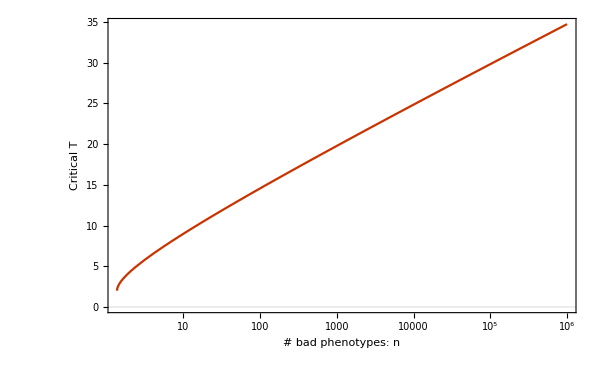

```mathematica
LogLinearPlot[-2 ProductLog[-1,-1/(2 n)],{n,Exp[1]/2,1000000},FrameLabel->{{"Critical T",},{"# bad phenotypes: n",}},ImageSize->600]
```

In this regime of small T and high n, where the approximation of re-distribution of non-adapted cells breaks down, we can get that the optimal switching rate is 0. Our Python-simulations show that this is an artefact. We therefore investigate for what parameter this happens, so that we can just set the switching rate to 0, thereby reducing the numerical errors that Mathematica makes in the optimisation process.

```mathematica
dntotdphi = FullSimplify[D[ntot[ϕ,f,p0sol[ϕ,f,T],T],ϕ]/.ϕ->0,{f>0,f<1,T>0}]
dGdphi = FullSimplify[D[G[ϕ,f,T],ϕ]/.ϕ->0,{f>0,f<1,T>0}]
```

((-1+f) (-1+√((-1+f)^2+4 ⅇ^T f)+f (-2 ⅇ^T-f+√((-1+f)^2+4 ⅇ^T f))) (1+ⅇ^T (-1+T)) ntot^(0,0,1,0)[0,f,(1+f-√((-1+f)^2+4 ⅇ^T f))/(2-2 ⅇ^T),T])/(2 (-1+ⅇ^T)^2 √((-1+f)^2+4 ⅇ^T f))+ntot^(1,0,0,0)[0,f,(1+f-√((-1+f)^2+4 ⅇ^T f))/(2-2 ⅇ^T),T]

(T+f^2 T-√((-1+f)^2+4 ⅇ^T f) T+f (-4+4 ⅇ^T-(2+√((-1+f)^2+4 ⅇ^T f)) T))/(2 √((-1+f)^2+4 ⅇ^T f) T)

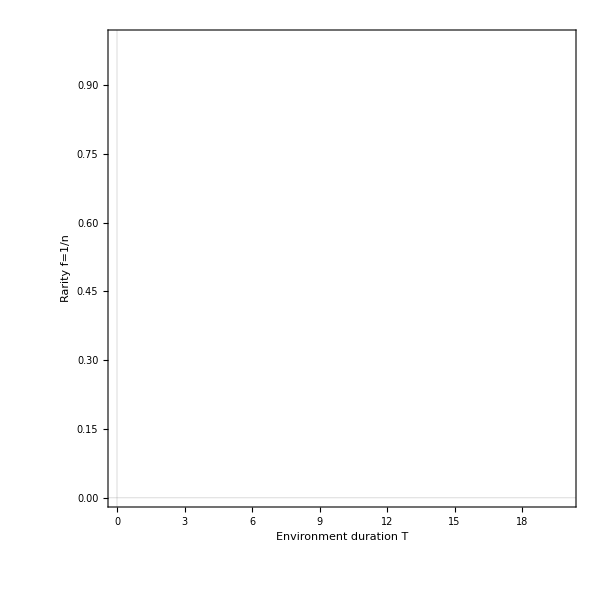

```mathematica
RegionPlot[Evaluate[dntotdphi]<0,{T,0,20},{f,0,1},PlotPoints->100,Frame->True, BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 18},ImageSize->600,FrameLabel->{"Environment duration T","Rarity f=1/n"}]
```

```mathematica
numerator[f_,T_]:=(1-f+√((-1+f)^2+4 ⅇ^T f)) (-2+(-1+f) T)-2 ⅇ^T (-1+f-√((-1+f)^2+4 ⅇ^T f)+T+f T)
fcrits[T_]:=f/.Solve[numerator[f,T]==0,f]
```

```mathematica
fcrits[T][[1]]
```

(4-8 ⅇ^T+4 ⅇ^(2 T)+4 T-4 ⅇ^T T+2 T^2-2 ⅇ^T T^2-√(-4 (2 T-2 ⅇ^T T+T^2+ⅇ^T T^2)^2+(-4+8 ⅇ^T-4 ⅇ^(2 T)-4 T+4 ⅇ^T T-2 T^2+2 ⅇ^T T^2)^2))/(2 (2 T-2 ⅇ^T T+T^2+ⅇ^T T^2))

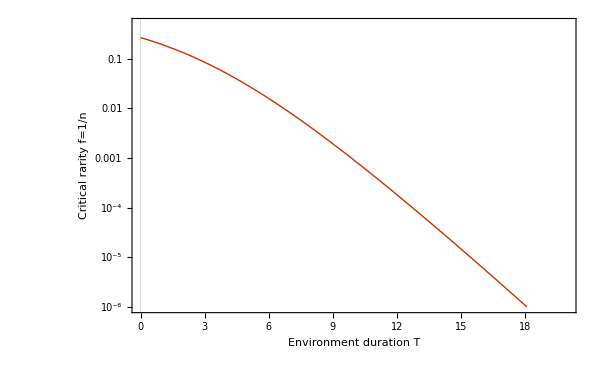

```mathematica
LogPlot[Evaluate[fcrits[T]][[1]],{T,0,20},FrameLabel->{"Environment duration T","Critical rarity f=1/n"}, PlotRange->{10^-6,0.5}, PlotStyle->{Thick},ImageSize->600]
```

Two conclusions: 1) For relatively short environment times, there is a minimal rarity (or maximal number of bad phenotypes) for which switching seems unfavourable. Our Python-simulations show that this is an artefact of our minimal model. This critical rarity goes down (more or less) exponentially. 2) It is clear, however, that switching always becomes favourable when the environment durations are long enough.

```mathematica
fcrit[T_]:=Evaluate[fcrits[T][[1]]]
```

### Optimal switching rates

We can now numerically maximise the average population growth rate, to find the optimal switching rate ϕ

```mathematica
pars3={T->10,f->0.1};
optphi[f_?NumericQ,T_?NumericQ] := If[f>=fcrit[T],ϕ/.Last[FindMaximum[Evaluate[Gnum[ϕ,f,T]],{ϕ,0.1,0,MAXPHI/.GLOBALPARS}]],0]
```

```mathematica
optphi[1/61,5.16538461538462]
Gnum[10^-9,1/61,5.16538461538462]
```

0

0.15751

A visual analysis shows that bet-hedging clearly gives a large fitness advantage, and that the optimal switching rates seem to go like 1/T for large enough T.

```mathematica
plotmaxG = Plot[Evaluate@Table[Gnum[optphi[f,T],f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[1/f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->n],FrameLabel->{"Environment Duration","average growth rate"},ImageSize->400,ImagePadding->{{60,5},{50,10}}];
plotzerophiG=Plot[Evaluate@Table[G[0,f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[1/f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->"ϕ=0"],PlotStyle->Dashed,FrameLabel->{"Environment Duration","average growth rate"},ImageSize->400,ImagePadding->{{60,5},{50,10}}];
plotargmaxphi = Plot[Evaluate@Table[optphi[f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[1/f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->n],FrameLabel->{"Environment Duration","Optimal switching rate (ϕ)"},ImageSize->400,ImagePadding->{{70,15},{50,20}}];
```

```mathematica
GraphicsColumn[{Show[plotmaxG,plotzerophiG],plotargmaxphi},ImageSize->800,Spacings->-30]
```

-Graphics-

### Limit for large environment durations

It is clear from the figures above that switching makes an important difference especially when T→Infinity. This may be surprising because the one parameter that differs between the two scenarios (ϕ>0 or ϕ=0) is decreasing such that they become more and more the same, while the results do not move closer. We will investigate this case a bit closer.

```mathematica
longTlimit=Limit[G[ϕ,f,T],T->Infinity,Assumptions->{f<1,f>0,ϕ>0}]
longTlimit/.ϕ->0
```

1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))

1

When we take the limit of T→ Infinity, we must make sure that ϕ is not zero. The case for ϕ=0 should be treated separately, because for this parameter setting our approximation that the non-adapted cells are re-distributed (that we mentioned above) does not hold. The minimal model therefore gives a growth rate of 1/2, while the actual evolutionary dynamics must give 1/(n+1), since all cells grow only when their preferred environment occurs, which is 1/(n+1) of the times. It is thus clear that for the large environment durations, the average growth rate for non-switching populations is over-estimated. For ϕ>0, we can however investigate what happens when we take the limit of T→Infinity. We know that the stable initial fraction p_0 will be f(1-(1/2(1+√(D)-fϕ-ϕ))), where D=1+ϕ (-2+ϕ+f (2+(2+f) ϕ)). For the total number of cells we have

```mathematica
Simplify[stot[ϕ,f,p0,T],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

(ⅇ^(-1/2 T (-1+√D+ϕ+f ϕ)) (√D (1+ⅇ^(√D T))+(-1+ⅇ^(√D T)) (-1+2 p0+ϕ+f ϕ)))/(2 √D)

But for large environment durations T only the term with exponentials will count, so we get for the total number of cells and the initial fraction:

```mathematica
stotLargeT =(ⅇ^(1/2 T (1+√D-ϕ-f ϕ))  (-1+2 p0+ϕ+f ϕ+√D))/(2 √D);
```

```mathematica
stotLargeT2 =Simplify[stotLargeT/.D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

(ⅇ^(1/2 T (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))) (-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))

One can check that the term in the exponential will always be positive. Let us now write down the average growth rate

```mathematica
GLargeT=1/T Log[Simplify[stotLargeT/.p0LargeT]]
```

Log[(ⅇ^(1/2 T (1+√D-(1+f) ϕ)) (-1-√D (-1+f)+f+ϕ+2 f ϕ+f^2 ϕ))/(2 √D)]/T

We can then get a function for the average growth rate in the large T-limit, with the initial fraction filled in:

```mathematica
GLargeTFullFun[ϕ_,T_,f_]:=Evaluate[GLargeT/.{D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))}]
GLargeTFullFun[ϕ,T,f]
```

Log[(ⅇ^(1/2 T (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (-1+f+ϕ+2 f ϕ+f^2 ϕ-(-1+f) √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))]/T

To investigate how this depends on the parameters for small ϕ, we can expand it in ϕ around 0:

```mathematica
Series[GLargeTFullFun[ϕ,T,f],{ϕ,0,1}]
```

Log[2 ⅇ^T f ϕ]/T+((3-3 f-2 T) ϕ)/(2 T)+O[ϕ]^2

We can then split this first term further to get for large T, and small ϕ:

```mathematica
smallPhiLargeT=1+Log[2f ϕ]/T;
```

So, the average growth rate will approximate 1 for very large T. Probably the most important long environment-time limit that we can take is when we pick ϕ = 1/T, because from our analytical derivations described in the paper and in the SI, it will turn out that this is the optimal switching rate. We see that in that case (as may be expected) the average growth rate goes to 1.

```mathematica
Limit[G[1/T,f,T],T->Infinity, Assumptions->{f>0,f<1}]
```

1

### Limit for very fast switching

For very fast switching we reach another model behaviour. The different switching rates will determine solely what the fraction of cells in the good phenotype will be. We see that p(T,ϕ,f) will become f/(1+f):

```mathematica
limFracLargePhi=Limit[frac[ϕ,f,p0,T],ϕ->Infinity,Assumptions->{f<1,f>0,p0<1,p0>0,T>0}]
```

f/(1+f)

And this will immediately also be the fixed point of p_0, since f(1-f/(1+f))=f/(1+f). So, we get

```mathematica
GLargePhi[ϕ_,f_,T_]:=Log[ntot[ϕ,f,f/(1+f),T]]/T
Limit[GLargePhi[ϕ,f,T],ϕ->Infinity,Assumptions->{f<1,f>0,T>0}]
```

Limit[Log[ntot[ϕ,f,f/(1+f),T]]/T,ϕ→∞,Assumptions→{f<1,f>0,T>0}]

The average growth rate at very fast switching is thus simply given by f/(1+f)=(1/n)/(1+1/n)=n/(1+n).

## Introducing Growth Rate Dependent Stability

The system with GRDS is essentially the same as before, but now we have two different switching rates: 1) a rate of switching away from adapted phenotypes ϕ_μ, and 2) a rate of switching away from non-adapted phenotypes ϕ_0, where ϕ_0=ϕ_μ r_μ, with r_μ>1. We will sometimes follow the notation in the paper and just use ϕ:=ϕ_μ and r:=r_μ. In this notebook we will also often use f_μ=1/r_μ, where 0<f_μ<1, because this makes it easier for Mathematica to derive some results.  Since the system with GRDS is essentially the same as before, we can reuse some of the derivations from above by using the temporary parameters f_g=f/f_μ:

```mathematica
analyticalSolGRDS = DSolve[{sg'[t] == (1 -phi) sg[t]+fg phi sb[t],sb'[t]== -fg phi sb[t]+phi sg[t],sg[0]==p0 ,sb[0]==(1-p0) },{sg[t],sb[t]},t];
analyticalSol2GRDS = FullSimplify[analyticalSolGRDS,Assumptions -> {p0>0,p0<1,fg>0,phi>0,t≥0}];
```

Again, we gather the number of cells in the good and bad phenotypes in a vector, and take the dot product with [1,1] to obtain the total number of cells.

```mathematica
sGRDS[phi_,fg_,p0_,t_]:=Evaluate[{sg[t],sb[t]}/.analyticalSol2GRDS[[1]]]
stotGRDS[phi_,fg_,p0_,t_]:=Evaluate[FullSimplify[sGRDS[phi,fg,p0,t].{1,1},Assumptions->{phi>0,t≥0,p0>0,p0<1,fg>0}]]
```

This gives us the ingredients for an expression of the fraction of good cells:

```mathematica
fracGRDS[phi_,fg_,p0_,t_]:=Evaluate[FullSimplify[sGRDS[phi,fg,p0,t][[1]]/stotGRDS[phi,fg,p0,t],Assumptions -> {fg>0,p0>0,p0<1,phi>0,t>=0}]]
fracGRDSNum[ϕ_?NumericQ,f_?NumericQ,fmu_?NumericQ,p0_?NumericQ,T_?NumericQ]:=Evaluate[fracGRDS[ϕ, f/fmu,p0,T]]
fracGRDSnewPars[ϕ_,f_,fmu_,p0_,T_]:=fracGRDS[ϕ,f/fmu,p0,T]
```

### Finding the initial fraction as a fixed point of the recursive formula

Again we find an initial fraction p0 by finding the fixed-point of the recursive equation p_0^new=f(1-p(T,... ,p_0^old). Note that this is the first time that the GRDS model differs from the conventional model by more than just a parameter change. The initial conditions are still given by the same formula, so that f is not replaced by f/f_μ here.

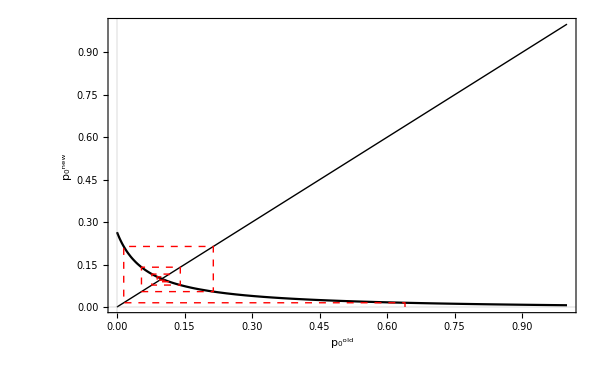

```mathematica
CobwebPlot[f(1-fracGRDSnewPars[ϕ,f,fmu,#,T])/.{ϕ->0.02,f->0.33,fmu->0.5,T->3}&,0.64,10,{0,1},PlotRange->{{0,1},{0,1}},Frame->True,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None,FrameLabel->{{"p_0^new",},{"p_0^old",""}},ImageSize->600]
```

```mathematica
p0solsGRDS=Solve[(1-fracGRDSnewPars[ϕ,f,fmu,p0,T])f == p0,p0];
p0solsGRDS/.{ϕ->0.25,f-> 0.1,fmu->0.5,T-> 30}
```

{{p0→0.0234669},{p0→-0.0653312}}

Again, it is clear that we want to go with the first solution, so let’s keep that one:

```mathematica
p0solGRDS[ϕ_,f_,fmu_,T_]:=Evaluate[p0/.p0solsGRDS[[1]]]
```

### Defining the average growth rate function

We can insert this starting fraction in our function for the total number of cells (s_tot), or we can immediately calculate the average growth rate:

```mathematica
GGRDSsimplified=FullSimplify[Log[stotGRDS[ϕ,f/fmu,p0solGRDS[ϕ,f,fmu,T],T]]/T,Assumptions->{ϕ>0,f<1,f>0,fmu>0,fmu<1,T>0}];
```

```mathematica
GGRDS[ϕ_,f_,fmu_,T_]:=Evaluate[GGRDSsimplified]
GnumGRDS[ϕ_?NumericQ,f_?NumericQ,fmu_?NumericQ,T_?NumericQ]:=Evaluate[GGRDSsimplified]
```

```mathematica
Manipulate[Plot[Evaluate[GGRDS[ϕ,1/n,1/r,T]]/.{r->rslide,n->nslide,T->Tslide},{ϕ,0,3}/.{T->Tslide},Frame->True,FrameStyle->Black,PlotRange->{0,1},FrameLabel -> {"Switching rate ϕ","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{rslide,10},1,100},{{nslide,200},1,1000},{{Tslide,10},0.00001,20}]
```

### The optimal switching rate for both cases

We can investigate how much difference GRDS can maximally make by optimising the switching rates (ϕ) in both cases. We use an upper bound for phi of 1000 currently, because it will generally not matter if this is 1000 or even larger.

```mathematica
optphi[f_?NumericQ,T_?NumericQ] := If[f>=fcrit[T],ϕ/.Last[FindMaximum[Evaluate[Gnum[ϕ,f,T]],{ϕ,0.1,0,MAXPHI/.GLOBALPARS}]],0]
optphiGRDSAlt=Function[{f,fmu,T},Quiet[
phiopt=ϕ/.Last[FindMaximum[GnumGRDS[ϕ,f,fmu,T],{ϕ,1/T/.pars,0,MAXPHI/.GLOBALPARS}]];
opt1 =GnumGRDS[phiopt,f,fmu,T];
opt2=GnumGRDS[MAXPHI/.GLOBALPARS,f,fmu,T];
If[opt1>opt2,phiopt,MAXPHI/.GLOBALPARS],
{FindMaximum::lstol}]
];
optphiGRDSWrapper[f_?NumericQ,fmu_?NumericQ,T_?NumericQ]:=optphiGRDSAlt[f,fmu,T]
```

### The limiting fraction for large T

We can again look at the limiting fraction for large T

```mathematica
largeTlimitGRDS = Limit[fracGRDSnewPars[ϕ,f,fmu,p0,t],t->Infinity,Assumptions->{ϕ>0,p0<1,p0>0,f>0,f<1,fmu<1,fmu>0}]
```

(-f (-2+p0) ϕ+fmu p0 (1-ϕ+√(1+(-2+(2 f)/fmu) ϕ+((f+fmu)^2 ϕ^2)/fmu^2)))/(f ϕ+fmu (-1+2 p0+ϕ+√(1+(-2+(2 f)/fmu) ϕ+((f+fmu)^2 ϕ^2)/fmu^2)))

And we can check if it is still independent of p0. We use our manually obtained expression to check with Mathematica’s expression

```mathematica
p0LargeTGRDS =Simplify[1/2 (1+√D-f ϕ/fmu-ϕ)/.{D-> 1+ϕ (-2+ϕ+f/fmu (2+(2+f/fmu) ϕ ))}]
FullSimplify[largeTlimitGRDS==1/2 (1+√D-f ϕ/fmu-ϕ ),D==1+ϕ (-2+ϕ+f/fmu (2+(2+f/fmu) ϕ))]
```

1/2 (1-ϕ-(f ϕ)/fmu+√(1+ϕ (-2+ϕ+(f (f ϕ+2 fmu (1+ϕ)))/fmu^2)))

True

Let’s compare this with the original limiting fraction. We can plot this function as a function of the switching rate from adapted phenotypes, and as a function from the switching rate from non-adapted phenotypes. We present both below.

```mathematica
p0LargeTnoGRDS = Simplify[1/2 (1+√D-f ϕ-ϕ)/.{D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))}]
```

1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))

```mathematica
parsGRDS={f->fslide,fmu->fmuslide,T->20,p0->0.1};
Manipulate[Plot[{1/2 (1-ϕ-(f ϕ)/fmu+√(1+ϕ (-2+ϕ+(f (f ϕ+2 fmu (1+ϕ)))/fmu^2)))/.{fmu->1/r,p0->0.1},1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))/.{p0->0.1}},{ϕ,0.001,3},FrameLabel->{{"long T-limit of fraction p(T)",},{"Switching rate Cell["ϕ",ExpressionUUID->"f15ce91e-2204-4df9-bb19-15b016369675"] from adapted phenotypes",}},PlotLegends->Placed[{StringForm["GRDS: r=``",r],"Original: r=1"},{0.8,0.8}],ImageSize->600],{{f,0.1},0.001,0.999},{{r,5},1.001,1000}]
```

```mathematica
Manipulate[Plot[{1/2 (1-ϕn-(f ϕn)/fmu+√(1+ϕn (-2+ϕn+(f (f ϕn+2 fmu (1+ϕn)))/fmu^2)))/.{ϕn -> ϕ/r,fmu->1/r,p0->0.1},1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))/.{p0->0.1}},{ϕ,0.001,3},FrameLabel->{{"long T-limit of fraction p(T)",},{"Switching rate rCell["ϕ",ExpressionUUID->"b247dfa3-e592-4787-9abf-0724f3cfec54"] from non-adapted phenotypes",}},PlotLegends->Placed[{StringForm["GRDS: r=``",r],"Original: r=1"},{0.8,0.8}],ImageSize->600],{{f,0.1},0.001,0.999},{{r,5},1.001,1000}]
```

### Limit for very fast switching

As before without GRDS, if switching is very fast, the fraction of cells in the adapted phenotype is determined solely by the difference in switching rate. This results in the following fraction of adapted cells, and thus also in this average population growth rate:

```mathematica
limFracLargePhiGRDS=Limit[fracGRDSnewPars[ϕ,f,fmu,p0,T],ϕ->Infinity,Assumptions->{f<1,f>0,fmu<1,fmu>0,p0<1,p0>0,T>0}]
```

f/(f+fmu)

And in the parameters used in the paper this becomes:

```mathematica
Simplify[f/(f+fmu)/.{f->1/n,fmu->1/r}]
```

r/(n+r)

## Analysis of difference with and without GRDS

From this point on, we will again return to the parameters as used in the paper, i.e. r=1/f_μ gives the factor difference between fast and slow switching (captures the strength of GRDS), n=1/f give the number of non-adapted phenotypes (captures the difficulty of the adaptation problem). Again ϕ captures the switching rate from fast growing to slow growing cells, and rϕ is the reverse switching rate.

### Some visual examinations of the average growth rate as function of parameters

In the slider-plot below, one can see that a high r (high difference in switching rates) usually increases the growth rates.

```mathematica
Manipulate[Plot[Evaluate[GGRDS[ϕ,1/n,1/r,T]]/.{r->rslide,n->nslide,T->Tslide},{ϕ,0.01,10/T}/.{T->Tslide},Frame->True,FrameStyle->Black,PlotRange->{0,1},FrameLabel -> {"Switching rate ϕ","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{rslide,70},1,1000},{{nslide,200},1,1000},{{Tslide,10},0.01,20}]
```

It would be useful to know whether the optimal r is always as high as possible. This seems indeed to be the case.

```mathematica
Manipulate[Plot[Evaluate[GGRDS[ϕ,1/n,1/r,T]]/.{ϕ->phislide,n->nslide,T->Tslide},{r,1,1000},PlotRange->Full,Frame->True,FrameStyle->Black,FrameLabel -> {"Strength of GRDS (r)","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{phislide,0.1},0.001,3},{{nslide,10},10,1000},{{Tslide,10},0.01,20}]
```

### The effect of r

What is the effect of growth rate dependent switching. In many cases, the stronger GRDS is, the better. To show this, we start from the optimal switching rate for the original model, and try if it becomes any better if we add some growth rate dependence. It is clear that for all tested parameters, the growth rates increase with GRDS.

```mathematica
p1=Plot[Evaluate@Table[Log[GnumGRDS[optphi[1/n,T],1/n,10^-logr,T]/Gnum[optphi[1/n,T],1/n,T]]/.{T->20},{n,{1,10,100,1000}}],{logr,-1,3},PlotLegends->LineLegend[Table[n,{n,{1,10,100,1000}}],LegendLabel->"n"],FrameLabel->{{"Log(G_GRDS/G_bet)",},{"log(r)",""}},ImageSize->400,ImagePadding->{{100,20},{80,20}}];
p2=Plot[Evaluate@Table[Log[GnumGRDS[optphi[1/n,T],1/n,10^-logr,T]/Gnum[optphi[1/n,T],1/n,T]]/.{n->10},{T,{1,2,5,10,100}}],{logr,-1,3},PlotLegends->LineLegend[Table[T,{T,{1,2,5,10,100}}],LegendLabel->T],FrameLabel->{{"Log(G_GRDS/G_bet)",},{"log(r)",""}},ImageSize->400,ImagePadding->{{100,20},{80,20}}];
GraphicsColumn[{p1,p2},ImageSize->600,Spacings->-40]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

From this, it seems relatively clear that GRDS can give a clear initial advantage. Also, it seems that larger r will always give a larger advantage. So let’s use this in the optimisation, we will set r to some upper bound

### Contourplots showing average growth rate as function of the three parameters

We analyse the effect of the three parameters 1) r, 2) T, 3) n, by making contourplots of 2-D slices of the three-dimensional parameter space.

#### Make function for getting time dynamics for given parameter set

Sometimes, we will want to highlight a certain parameter set. Here is a function that does that for us.

```mathematica
getTimeDynamics=Function[{N,r,T,color,imagesize},
Quiet[f=1/N;fmu=1/r;
optphi=optphiGRDSWrapper[f,fmu,T];
pt=Plot[fracGRDSNum[optphi ,f,fmu,p0solGRDS[optphi,f,fmu,T],t],{t,0,T},PlotStyle->{Thickness[0.02],LineColor->color},ImagePadding->{{40,10},{120,40}},PlotRange->{{0,T},{0,1}},FrameLabel->{{"Adapted fraction",},{"Time",Style[StringForm["T=``, n=``, r=``",Round[T],Round[N],Round[r]],Bold]}},ImageSize->imagesize],{FindMaximum::lstol}];
{optphi,pt}];
```

#### Contourplots showing effects of r and n

We define a general plotting function that makes a contourplot of the average growth rate depending on the strength of GRDS, and the complexity of the regulation problem captured by the number of bad phenotypes n.

```mathematica
makeMuContourPlotFmuN=Function[{T,plotpoints,imagesize},
ContourPlot[GnumGRDS[optphiGRDSWrapper[10^-logn,10^-logr,T],10^-logn,10^-logr,T],{logr,0,3},{logn,0,3},ColorFunction->(ColorData["M10DefaultDensityGradient"][0+1#]&),ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},FrameLabel->{{"# of bad phenotypes: n",},{"Strength of GRDS: r",Style[StringForm["Average growth rate if T=``",T],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{0,1}},{Automatic,11},LegendMarkerSize->200,LegendMargins->{{-40,0},{0,0}}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}]];
```

Here follows an example:

```mathematica
contPlot1 = makeMuContourPlotFmuN[.1,20,400];
contPlot2 = makeMuContourPlotFmuN[1,20,400];
contPlot3 = makeMuContourPlotFmuN[10,20,400];
contPlot4 = makeMuContourPlotFmuN[100,20,400];
```

```mathematica
GraphicsGrid[{{contPlot1,contPlot2},{contPlot3,contPlot4}},ImageSize->900,Spacings->0]
```

-Graphics-

It is instructive to also see what the optimal switching rates ϕ are in these contour plots. We will see that there is an abrupt change in parameter space, where the optimal behaviour goes from slow switching, where ϕ~1/T, to very fast switching, where ϕ→Infinity. We plot the bound that separates the long-T regime from the infinite-ϕ regime as a red line.

```mathematica
makeBoundPlotLongT=Function[NorT,Plot[Log10[10^logr/NorT],{logr,0,4},PlotRange->{-1,3},PlotStyle->{Thickness[0.01]}]];
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log10[x/min]/Log10[max/min]
makePhiContourPlotFmuN=Function[{T,plotpoints, imagesize},
Quiet[ContourPlot[optphiGRDSWrapper[10^-logn,10^-logr,T],{logr,0,3},{logn,0,3},PlotRange->{0.001,1000},ColorFunctionScaling->False,Contours->{0.01,0.1,1,10,100},ColorFunction->(ColorData["M10DefaultDensityGradient"][LogarithmicScaling[#,0.001,1000]]&),FrameLabel->{{"# of bad phenotypes: n",},{"Fold change switching rate: r",Style[StringForm["Optimal switching rate (Cell["ϕ",ExpressionUUID->"5f69a636-cc3a-4654-b7cc-5def8541495f"]) if T=``",T],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{ColorData["M10DefaultDensityGradient"],{0,1}},LegendMarkerSize->200,LegendMargins->{{-40,0},{0,0}},"Ticks"->({LogarithmicScaling[#,0.001,1000],#}&/@(0.001 (1000/0.001)^Range[0,1,1/6]))],PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}],{FindMinimum::reged,FindMaximum::lstol,FindMaximum::nrnum}]];
```

```mathematica
contPlot1Phirvsn = makePhiContourPlotFmuN[.1,20,400];
contPlot2Phirvsn = makePhiContourPlotFmuN[1,20,400];
contPlot3Phirvsn = makePhiContourPlotFmuN[10,20,400];
contPlot4Phirvsn = makePhiContourPlotFmuN[100,20,400];
```

```mathematica
GraphicsGrid[{{Show[contPlot1Phirvsn,makeBoundPlotLongT[.1]],Show[contPlot2Phirvsn,makeBoundPlotLongT[1]]},{Show[contPlot3Phirvsn,makeBoundPlotLongT[10]],Show[contPlot4Phirvsn,makeBoundPlotLongT[100]]}},ImageSize->950,Spacings->0]
```

-Graphics-

#### Contourplots showing effects of r and T

We also define a general plotting function that makes a contourplot of the average growth rate depending on the strength of GRDS, and the average duration of the environments.

```mathematica
makeMuContourPlotFmuT=Function[{N,plotpoints,imagesize,logrub},
ContourPlot[GnumGRDS[optphiGRDSWrapper[1/N,10^-logr,10^logT],1/N,10^-logr,10^logT],{logr,0,logrub},{logT,-1,3},ColorFunction->(ColorData["M10DefaultDensityGradient"][0+1#]&),ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},FrameLabel->{{"Environment duration: T",},{"Strength of GRDS: r",Style[StringForm["Average growth rate if # bad phens=``",N],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{0,1}},{Automatic,11},LegendMarkerSize->200,LegendMargins->{{-40,0},{0,0}}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}]];
```

Here follows an example:

```mathematica
contPlot1 = makeMuContourPlotFmuT[1,20,400,3];
contPlot2 = makeMuContourPlotFmuT[10,20,400,3];
contPlot3 = makeMuContourPlotFmuT[100,20,400,3];
contPlot4 = makeMuContourPlotFmuT[1000,20,400,3];
```

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,999.} in coordinate 1 and the computed search direction points outside the region.

```mathematica
GraphicsGrid[{{contPlot1,contPlot2},{contPlot3,contPlot4}},ImageSize->900,Spacings->0]
```

-Graphics-

Again it is instructive to see the behaviour of the optimal switching rate ϕ in these contour plots

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log10[x/min]/Log10[max/min]
makePhiContourPlotFmuT=Function[{N,plotpoints, imagesize},
Quiet[ContourPlot[optphiGRDSWrapper[1/N,10^-logr,10^T],{logr,0,4},{T,-1,3},PlotRange->{0.001,1000},Contours->{0.01,0.1,1,10,100},ColorFunctionScaling->False,ColorFunction->(ColorData["M10DefaultDensityGradient"][LogarithmicScaling[#,0.001,1000]]&),FrameLabel->{{"Environment duration: T",},{"Fold change switching rate: r",
Style[StringForm["Opt switch rate (ϕ) if # bad phens=``",N],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{ColorData["M10DefaultDensityGradient"],{0,1}},LegendMarkerSize->200,LegendMargins->{{-40,0},{0,0}},"Ticks"->({LogarithmicScaling[#,0.001,1000],#}&/@(0.001 (1000/0.001)^Range[0,1,1/6]))],PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}],{FindMinimum::reged,FindMaximum::lstol,FindMaximum::nrnum}]];
```

```mathematica
contPlot1PhirvsT = makePhiContourPlotFmuT[1,20,400];
contPlot2PhirvsT = makePhiContourPlotFmuT[10,20,400];
contPlot3PhirvsT = makePhiContourPlotFmuT[100,20,400];
contPlot4PhirvsT = makePhiContourPlotFmuT[1000,20,400];
```

```mathematica
GraphicsGrid[{{Show[contPlot1PhirvsT,makeBoundPlotLongT[1]],Show[contPlot2PhirvsT,makeBoundPlotLongT[10]]},{Show[contPlot3PhirvsT,makeBoundPlotLongT[100]],Show[contPlot4PhirvsT,makeBoundPlotLongT[1000]]}},ImageSize->950,Spacings->0]
```

-Graphics-

#### The optimal switching rates for T relatively large

To get some insight in the dependence of the optimal switching rate on the parameters, we plot G as a function of ϕ for different parameter sets.

```mathematica
plotPhiVSG=Function[{n,T},
Quiet[
rs={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/n,1/r,T],{r,rs}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[r,{r,rs}],LegendLabel->Style[r,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ",StringForm["n = ``, T = ``",n,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/n,1/rs[[ii]],T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/n,1/rs[[ii]],T]}]},{ii,1,5}]}]];
plotPhiVSGvaryT=Function[{n,r},
Quiet[
Ts={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/n,1/r,T],{T,Ts}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->Style[T,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ",StringForm["n = ``, r = ``",n,r]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/n,1/r,Ts[[ii]]],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/n,1/r,Ts[[ii]]]}]},{ii,1,5}]}]];
plotPhiVSGvaryN=Function[{r,T},
Quiet[
ns={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/n,1/r,T],{n,ns}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[n,{n,ns}],LegendLabel->Style[n,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ",StringForm["r = ``, T = ``",r,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/ns[[ii]],1/r,T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/ns[[ii]],1/r,T]}]},{ii,1,5}]}]];
```

Because the figures below (on the left) indicate that the switching rate away from non-adapted phenotypes tends to follow ϕ_=1/T, we also plot G dependent on ϕ T.

```mathematica
plotPhiRmuTVSG=Function[{n,T},
Quiet[
rs={1,5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiT/T,1/n,1/r,T],{r,rs}],{phiT,10^-3,10},PlotLegends->LineLegend[Table[r,{r,rs}],LegendLabel->Style[r,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕT",StringForm["n = ``, T = ``",n,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/n,1/rs[[ii]],T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]T,GGRDS[optphis[[ii]],1/n,1/rs[[ii]],T]}]},{ii,1,5}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
plotPhiRmuTVSGvaryT=Function[{n,r},
Quiet[
Ts={1,5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiT/T,1/n,1/r,T],{T,Ts}],{phiT,10^-3,10},PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->Style[T,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕT",StringForm["Cell["n",ExpressionUUID->"ace202ca-dfce-482f-af29-7deabaec1239"] = ``, r = ``",n,r]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/n,1/r,Ts[[ii]]],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]Ts[[ii]],GGRDS[optphis[[ii]],1/n,1/r,Ts[[ii]]]}]},{ii,1,5}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
plotPhiRmuTVSGvaryN=Function[{r,T},
Quiet[
ns={5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiT/T,1/n,1/r,T],{n,ns}],{phiT,10^-3,10},PlotLegends->LineLegend[Table[n,{n,ns}],LegendLabel->Style[n,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕT",StringForm["r = ``, T = ``",r,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDSWrapper[1/ns[[ii]],1/r,T],{ii,1,4}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]T,GGRDS[optphis[[ii]],1/ns[[ii]],1/r,T]}]},{ii,1,4}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
```

```mathematica
pars={logn->2,logT->N[Log10[20]]};
ptphiG=plotPhiVSG[10^logn/.pars,10^logT/.pars];Print["First done."];
ptphiRmuTG=plotPhiRmuTVSG[10^logn/.pars,10^logT/.pars];Print["Second done."];
pars={logn->2,logr->1};
ptphiGvaryT=plotPhiVSGvaryT[10^logn/.pars,10^logr/.pars];Print["Third done."];
ptphiRmuTGvaryT=plotPhiRmuTVSGvaryT[10^logn/.pars,10^logr/.pars];Print["Fourth done."];
pars={logT->N[Log10[20]],logr->1};
ptphiGvaryN=plotPhiVSGvaryN[10^logr/.pars,10^logT/.pars];Print["Fifth done."];
ptphiRmuTGvaryN=plotPhiRmuTVSGvaryN[10^logr/.pars,10^logT/.pars];Print["Sixth done."];
```

First done.

Second done.

Third done.

Fourth done.

Fifth done.

Sixth done.

```mathematica
GraphicsGrid[{{ptphiG,ptphiRmuTG},{ptphiGvaryT,ptphiRmuTGvaryT},{ptphiGvaryN,ptphiRmuTGvaryN}},ImageSize->1500,Spacings->-40]
```

-Graphics-

#### An approximate expression for the average growth rate for T>r/n

From the derivations in the SI we know that under some assumptions (large enough T and small enough switching rates), the optimal switching rate is well-approximated by ϕ^opt~1/T, and that the average growth rate behaves like G~1-1/T-Log[nT/(1+r)]. In the following plots we see that this approximation holds for a large range of parameters: more or less until the predicted growth rate approaches the theoretical maximum of 1.

```mathematica
getGGRDSandFit=Function[{T},
ns={5,50,500};
pt1 = LogLogPlot[Evaluate@Table[GnumGRDS[optphiGRDSWrapper[1/n,1/r,T],1/n,1/r,T],{n,ns}],{r,1.,100000.},FrameLabel->{{"Average growth rate: G",},{"Strength of GRDS: r",Style[StringForm["Average growth rate if T=``",T],Bold]}},PlotLegends->LineLegend[Table[n,{n,ns}],LegendLabel->Style[n,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],ImageSize->400];
pt2= LogLogPlot[Evaluate@Table[(1-1/T-Log[n]/T-Log[T/2]/T+Log[(1+r)/2]/T),{n,ns}],{r,1.,10000.},PlotStyle->Dashed,FrameLabel->{{"Average growth rate: G",},{"Strength of GRDS: r",Style[StringForm["Average growth rate if T=``",T],Bold]}},ImageSize->400];
Show[pt1,pt2]
];
```

```mathematica
GGRDSandFitT10 =getGGRDSandFit[10];Print["First done."];
GGRDSandFitT20 =getGGRDSandFit[20];Print["Second done."];
GGRDSandFitT40 =getGGRDSandFit[40];Print["Third done."];
GGRDSandFitT80 =getGGRDSandFit[80];
```

First done.

Second done.

Third done.

```mathematica
GraphicsGrid[{{GGRDSandFitT10,GGRDSandFitT20},{GGRDSandFitT40,GGRDSandFitT80}},ImageSize->1100,Spacings->0]
```

-Graphics-

```mathematica
ptMuContourFmuTN100=makeMuContourPlotFmuT[100,20,400,4];
ptPhiContourFmuTN100=makePhiContourPlotFmuT[100,20, 400]; (*The plotting of optimal phi is very slow, therefore we only take 3 plotpoints. Increase this for higher resolution.*)
```

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,999.} in coordinate 1 and the computed search direction points outside the region.

### Combining contourplots with time dynamics

We define some functions that combine a contourplot showing dependence of average growth rates on parameters, with some highlighted time dynamics for specific parameter sets.

```mathematica
getContourPlusTimeDynamicsFmuNAdapted=Function[{T,plotpoints,parsSets},
contourfmuN=makeMuContourPlotFmuN[T,plotpoints,400];
pos=Table[{Log10[r],Log10[N]}/.parsSets[[i]],{i,1,3}];
posInfos=Table[getTimeDynamics[N/.parsSets[[i]],r/.parsSets[[i]],T,apple4[[i]],300],{i,1,3}];
contour=Show[contourfmuN,Epilog->{PointSize[0.05],Table[{apple4[[ii]],Point[pos[[ii]]]},{ii,1,3}],Table[Text[StringForm[" ϕ = `` ",Round[posInfos[[j]][[1]]/.parsSets[[j]],0.0001]],Offset[{10,0},pos[[j]]],{Left,Center},Background->None,BaseStyle->{FontFamily->"Helvetica",Black}],{j,1,3}]}];
inset=GraphicsRow[Table[posInfos[[k]][[2]],{k,1,2}],ImageSize->400,Spacings->-80];
GraphicsColumn[{contour,inset},ImageSize->800,Spacings->-90]];
```

```mathematica
getContourPlusTimeDynamicsFmuTAdapted=Function[{N,plotpoints,parsSets},
contourfmuT=makeMuContourPlotFmuT[N,plotpoints,400];
pos=Table[{Log10[r],Log10[T]}/.parsSets[[i]],{i,1,3}];
posInfos=Table[getTimeDynamics[N,r/.parsSets[[i]],T/.parsSets[[i]],apple4[[i]],300],{i,1,3}];
contour=Show[contourfmuT,Epilog->{PointSize[0.05],Table[{apple4[[ii]],Point[pos[[ii]]]},{ii,1,3}],Table[Text[StringForm[" ϕ = `` ",Round[posInfos[[j]][[1]]/.parsSets[[j]],0.0001]],Offset[{10,0},pos[[j]]],{Left,Center},Background->None,BaseStyle->{FontFamily->"Helvetica",Black}],{j,1,3}]}];
inset=GraphicsRow[Table[posInfos[[k]][[2]],{k,1,2}],ImageSize->400,Spacings->-80];
GraphicsColumn[{contour,inset},ImageSize->800,Spacings->-90]];
```

```mathematica
parsSetsTimeDynamicsfmuT={{r->10^2,T->10^1},{r->10^1,T->10^2},{r->10^1,T->10^1}};
parsSetsTimeDynamicsfmuN={{N->10^1,r->10^1},{N->10^2,r->10^1},{N->10^2,r->10^2}};
apple4={green,red,grey,purple};
contourTimeDynamicsT10combined=getContourPlusTimeDynamicsFmuNAdapted[10,20,parsSetsTimeDynamicsfmuN];Print["Done first."];
apple4={grey,purple,red,green};
contourTimeDynamicsN100combined=getContourPlusTimeDynamicsFmuTAdapted[100,20,parsSetsTimeDynamicsfmuT];
```

Done first.

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,1000.} in coordinate 1 and the computed search direction points outside the region.

```mathematica
GraphicsRow[{contourTimeDynamicsT10combined,contourTimeDynamicsN100combined},ImageSize->1600,Spacings->-80]
```

-Graphics-